```mathematica
ClearAll["`*"]
```

### This notebook will ONLY comprise a comparison of κ to the minimum error of various types of LMMs

```mathematica
ρ[a_][xi_]:=Sum[a[[i+1]] xi^i,{i,0,Length[a]-1}]
σ[b_][xi_]:=Sum[b[[i+1]] xi^i,{i,0,Length[b]-1}]
```

### Scenario 1: 2-step LMMs (all β coefficients are nonzero)

```mathematica
cond2step=((β0-β1+β2) (-2+β0+β1+β2)≤0&&(2+β0-β1-3 β2) (β0+β1+β2)≤0&&((4 β0 β2>β1^2&&β0≠β2)||β0^2+β1^2+β2^2≥6 β0 β2))&&(Abs[β2 κ^2]>Abs[β0]&&Abs[β0^2-β2^2 κ^4]>Abs[β1 κ (β0-β2 κ^2)])/.{β0->-2+β1+3 β2}//Simplify;
```

```mathematica
(Abs[β2 κ^2]>Abs[β0]&&Abs[β0^2-β2^2 κ^4]>Abs[β1 κ (β0-β2 κ^2)])/.{β0->-2+β1+3 β2}//Simplify
```

```mathematica
Abs[β2 κ^2]>Abs[β0]&&Abs[β0^2-β2^2 κ^4]>Abs[β1 κ (β0-β2 κ^2)]//TeXForm
```

\left| \text{$\beta $2} \kappa ^2\right| >| \text{$\beta $0}| \land \left| \text{$\beta $0}^2-\text{$\beta $2}^2 \kappa ^4\right| >\left|
   \text{$\beta $1} \kappa  \left(\text{$\beta $0}-\text{$\beta $2} \kappa ^2\right)\right|

```mathematica
c3[a_,b_]:=Abs[1/(σ[b][1])Sum[(j^3 a[[j+1]])/(3!)-(j^(3-1)b[[j+1]])/((3-1)!),{j,0,Length[a]-1}]]
```

```mathematica
c3[{3-2 β1-4 β2,-4+2 β1+4 β2,1},{-2+β1+3 β2,β1,β2}]//Simplify
```

1/12 Abs[(-4+β1+8 β2)/(-1+β1+2 β2)]

```mathematica
c32step[β1_,β2_]:=1/12 Abs[(-4+β1+8 β2)/(-1+β1+2 β2)]
```

#### Because Mathematica can’t handle plotting this directly, we will just make a table and sample points from κ=0 to 1

```mathematica
κlist2=Table[{k,Quiet[Minimize[{c32step[β1,β2],cond2step/. κ->k},{β1,β2}][[1]]]},{k,0,1,1/100}];
```

#### Note that Minimize was used instead of NMinimize because the numerical process lead to inconsistencies

#### Because κ!=0, we will artificially add that in, as it corresponds to the BDF2 method

```mathematica
κlist2=κlist2/.κlist2[[1,2]]->1/3;
```

#### We now plot it below

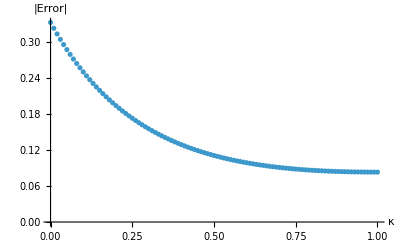

```mathematica
l1=ListPlot[κlist2,AxesLabel->{κ, "|Error|"}]
```

```mathematica
{c32step[β1,β2],cond2step/. κ->1/2}
```

{1/12 Abs[(-4+β1+8 β2)/(-1+β1+2 β2)],(-1+2 β2) (-2+β1+2 β2)≤0&&((4 β2 (-2+β1+3 β2)>β1^2&&β1+2 β2≠2)||2+β1^2≥2 β1+4 β2^2)&&Abs[β2]/4>Abs[-2+β1+3 β2]&&Abs[-β2^2/16+(-2+β1+3 β2)^2]>1/2 Abs[β1 (-2+β1+(11 β2)/4)]}

```mathematica
cond2step2=((β0-β1+β2) (-2+β0+β1+β2)≤0&&(2+β0-β1-3 β2) (β0+β1+β2)≤0&&((4 β0 β2>β1^2)||β0^2+β1^2+β2^2≥6 β0 β2))&&(Abs[β2 κ^2]>Abs[β0]&&Abs[β0^2-β2^2 κ^4]>Abs[β1 κ (β0-β2 κ^2)])/.{β0->-2+β1+3 β2}//Simplify
```

(-1+2 β2) (-2+β1+2 β2)≤0&&(4 β2 (-2+β1+3 β2)>β1^2||2+β1^2≥2 β1+4 β2^2)&&Abs[β2 κ^2]>Abs[-2+β1+3 β2]&&Abs[(-2+β1+3 β2)^2-β2^2 κ^4]>Abs[β1 κ (-2+β1+3 β2-β2 κ^2)]

```mathematica
FindMinimum[{c32step[β1,β2],cond2step2/. κ->1/2},{β1,β2}]
```

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

{0.0973469,{β1→0.57779,β2→0.517155}}

```mathematica
κlist3=Table[{k,Quiet[NMinimize[{c32step[β1,β2],cond2step/. κ->k},{β1,β2}][[1]]]},{k,0,1,1/10}];
```

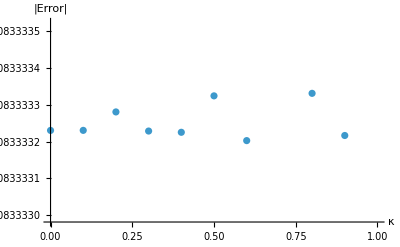

```mathematica
ListPlot[κlist3,AxesLabel->{κ, "|Error|"}]
```

#### Note that the upper and lower limit for the Error includes 1/3 where κ=0 (BDF2) and 1/12 where κ=1 (Trapezoidal Method)

### Scenario 2: 3-step LMMs (2 nonzero β coefficients)

```mathematica
c32beta[β2_,β3_]:=Module[
{a,b,sum},
a={-1+β2/2+(3 β3)/2,3-2 β2-4 β3,-3+(3 β2)/2+(5 β3)/2,1};
b={0,0,β2,β3};
sum=Abs[1/(σ[b][1])Sum[(j^3 a[[j+1]])/(3!)-(j^(3-1)b[[j+1]])/((3-1)!),{j,0,Length[a]-1}]];
sum//Simplify
]
```

```mathematica
cond2beta=((β3==1/2&&β2==1/2)||(1/2<β3<3/5&&1/2 (2-5 β3)+1/2 √(4+4 β3-15 β3^2)≤β2≤β3)||(β3==3/5&&0≤β2≤3/5)||(3/5<β3<2/3&&1/2 (2-5 β3)+1/2 √(4+4 β3-15 β3^2)≤β2≤β3)||(β3==2/3&&β2≥-2/3)||(2/3<β3<1&&-β3≤β2≤2-2 β3)||(β3==1&&-1≤β2≤0)||(1<β3<2&&-β3≤β2≤2-2 β3)||(β3==2&&β2==-2))&&Abs[β3 κ]^2>Abs[β2 β3 κ];
```

```mathematica
κlist=Table[{k,Quiet[Minimize[{c32beta[β2,β3],cond2beta/. κ->k},{β2,β3}][[1]]]},{k,0,1,1/100}];
```

#### Again we artificially add the first point where κ=0

```mathematica
κlist=κlist/.κlist[[1,2]]->1/6;
```

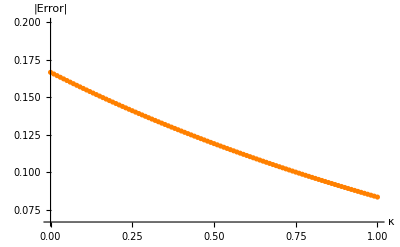

```mathematica
l2=ListPlot[κlist,AxesLabel->{κ, "|Error|"},PlotRange->{{0,1},{1/15,1/5}},PlotStyle->Orange]
```

### Let’s now compare the two graphs, along with the BDF-like 4 and 5-step LMMs

```mathematica
pt1={{0,5/6-1/(√2)}};
```

```mathematica
pt2={{0,1/3-1/(2 √5)}};
```

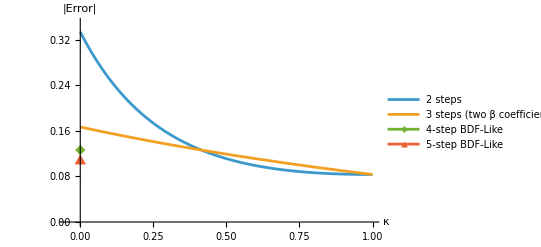

```mathematica
ListLinePlot[{κlist2,κlist,pt1,pt2},AxesLabel->{κ, "|Error|"},PlotRange->{{-.05,1},{0,.35}},PlotMarkers->{None,None,Automatic,Automatic},PlotLegends->{"2 steps","3 steps (two β coefficients)","4-step BDF-Like","5-step BDF-Like"}]
```

#### Something important to note here is that this behavior for the 3-step LMM with 2 nonzero coefficients does not show the behavior of general 3-step methods. For all 3-step LMMs, the behavior of the line will share the same two endpoints at κ=0 and 1, but the Abs[Error] will always remain less than the Abs[Error] for 2-step methods for the same κ value. This is because despite remaining 2^nd order accurate, a higher-step LMM will always have a smaller error than a lower-step LMM for the same value of κ

### Unfortunately, repeating the process for all 3-step methods is too much for Mathematica to handle.